```mathematica
(* see force_nondim_exp_and_linear.nb for the derivation of the force-velocity curves. *)
```

## Assumptions

### Parameters and rules

```mathematica
(* default parameters *)
ruleNonDim={pi3->1.,pi4->4.7,pi5->0.1,pi6->10};
```

### Force functions (exponential only)

```mathematica
fNonPrefND[U_]:=-(pi3+1)/(pi3(1-Exp[-pi5/(pi6 U)])+1) (Exp[pi4](1-Exp[pi5] Exp[-pi5/(pi6 U)])-(1-pi6 U)(1-Exp[-pi5/(pi6 U)]))/((1-pi6  U) (Exp[pi4]-1));
fPrefND[U_]:=-(1+pi6 U(Exp[pi4]-1)^-1)/(1-pi6 U);
```

### Down-preferred

```mathematica
fND[U_]:=If[U≥0,fNonPrefND[U],fPrefND[U]];
```

The opposite species, up-preferred, is given by -fExp[-U].

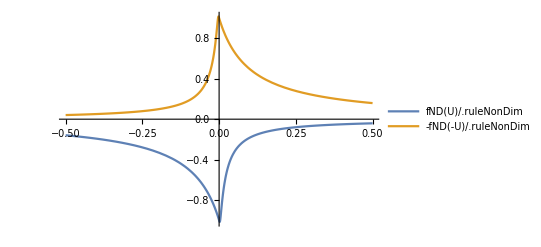

```mathematica
Plot[{fND[U]/.ruleNonDim,-fND[-U]/.ruleNonDim},{U,-.5,.5},PlotRange->All,PlotLegends->"Expressions"]
```

### Right-hand side of ODE

```mathematica
rhs[U_]:=-ϕ fND[-U]+(1-ϕ)fND[U]-ζ U;
```

### Solve for parameters in terms of U

```mathematica
phiSolRule=Solve[rhs[U]==0,ϕ][[1]];
zhatSolRule=Solve[rhs[U]==0/.ζ->1/zh,zh][[1]];
```

### Derivative of phi and zeta wrt U at U=0

```mathematica
(* slow *)
dpdU=Limit[D[ϕ/.phiSolRule,U],{U->0},Assumptions->pi3>0&&pi5>0&&pi6>0]
dzdU=Limit[D[zh/.zhatSolRule,U],{U->0},Assumptions->pi3>0&&pi5>0&&pi6>0]
```

(-ζ+ⅇ^pi4 (pi6+ζ))/(2 (-1+ⅇ^pi4))

1/(-1+2 ϕ)

### Derivative of F wrt U at U=0

```mathematica
Limit[D[-ϕ fND[-U]+(1-ϕ)fND[U]-ζ U,U],{U->0},Assumptions->pi4>0&&pi3>0&&pi5>0&&pi6>0]
```

(ζ-ⅇ^pi4 (pi6+ζ))/(-1+ⅇ^pi4)

```mathematica
Limit[D[fND[U],U],U->0]
```

$Aborted